67/135, 100/170, 76/167, 123/163, 147/202, 64/147, 102/168, 64/148, 194/258, 95/154

```mathematica
capas={{67,135},{100,170},{76,167},{123,163},{147,202},{64,147},{102,168},{64,148},{194,258},{95,154}}
```

{{67,135},{100,170},{76,167},{123,163},{147,202},{64,147},{102,168},{64,148},{194,258},{95,154}}

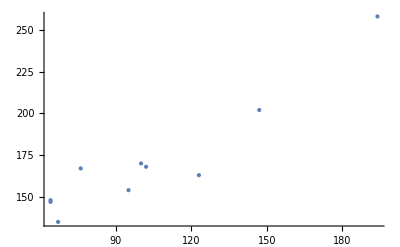

```mathematica
ListPlot[capas,PlotStyle->PointSize[Large]]
```

```mathematica
capasx=Table[capas[[i]][[1]],{i,Length[capas]}]
capasy=Table[capas[[i]][[2]],{i,Length[capas]}]
```

{67,100,76,123,147,64,102,64,194,95}

{135,170,167,163,202,147,168,148,258,154}

```mathematica
PearsonCorrelationTest[capasx,capasy]
```

PearsonCorrelationTest::nortst: At least one of the p-values in {0.361805,0.0106746}, resulting from a test for normality, is below 0.025. The tests in {PearsonCorrelation} require that the data is normally distributed.

0.0000665623

Amostra pequena demais?

```mathematica
capas[[1]][[1]]
```

67

```mathematica
capasdiv = Table[capas[[i]][[2]]/capas[[i]][[1]], {i, Length[capas]} ]
```

{135/67,17/10,167/76,163/123,202/147,147/64,28/17,37/16,129/97,154/95}

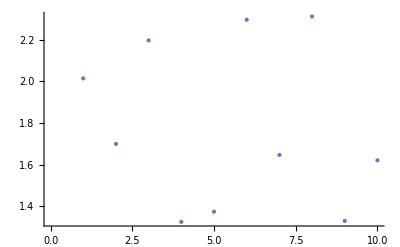

```mathematica
ListPlot[capasdiv,PlotStyle->PointSize[Large]]
```

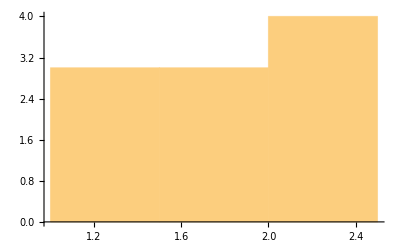

```mathematica
Histogram[capasdiv]
```

Mean: avg. Median: middle sorted value. Mode (commonest): most repeating value (many).

```mathematica
{N[Mean[capasdiv]],N[Median[capasdiv]],N[Commonest[capasdiv]]}//AccountingForm
```

{1.7819,1.67353,{2.01493,1.7,2.19737,1.3252,1.37415,2.29688,1.64706,2.3125,1.3299,1.62105}}

```mathematica
{N[Variance[capasdiv]],N[StandardDeviation[capasdiv]]}//AccountingForm
```

{0.15595,0.394905}

A média da razão de preço é 1.7. A “faixa de razão” com maiores valores é 2.0 - 2.5.

```mathematica
-Graphics-
-Graphics-
```